# StateMint Example

This notebook will focus on how to interact with StateMint in a Mathematica notebook.

Before we begin we need to import the StateMint package.

```mathematica
SetDirectory[NotebookDirectory[]];
<<StateMint`
```

Now that StateMint has been imported we can start working on a problem. In this case we will be working on the problem set forth in the tutorial. This problem consists of a motor powering a pump through a flexible shaft. This pump pushes water through an elbow with a known resistance and out into the atmosphere. A diagram of the physical system can be seen below.

The following equations for this system were found in the tutorial .

```mathematica
inVars={Vs[t]};
primaryVars = {
tk[t],
vR[t],
vL[t],
i1[t],
w2[t],
w3[t],
P4[t],
QR[t]
};
elementalEqs={
tk'[t]==kt wk[t],
vR[t]==R iR[t],
vL[t]==L iL'[t],
i1[t]==-Kv t2[t],
w2[t]==Kv v1[t],
w3[t]==Q4[t]/-DD,
P4[t]==t3[t]/DD,
QR[t]==PR[t]/Rf
};
constraintEqs={
iL[t]==i1[t],
iR[t]==i1[t],
t2[t]==-tk[t],
t3[t]==tk[t],
Q4[t]==QR[t],
v1[t]==Vs[t]-vR[t]-vL[t],
wk[t]==w2[t]-w3[t],
PR[t]==P4[t]
};
outExps={QR[t]};
```

Using the following command, the state equations can be found.

```mathematica
stateSolution=stateEquations[inVars,primaryVars,elementalEqs,constraintEqs]//Flatten;
stateVars = "state variables"/.stateSolution;
stateEqList = "RHS"/.stateSolution;
"state equations"/.stateSolution//TableForm
```

tk'[t]==((kt-DD^2 kt Kv^2 R Rf) tk[t])/(DD^2 (1+kt Kv^2 L) Rf)+(kt Kv Vs[t])/(1+kt Kv^2 L)

In a similar way, the output equations can be found.

```mathematica
outEqList=outEquations[inVars,stateVars,outExps,elementalEqs~Join~constraintEqs];
outEqList//Thread[Table[y[i],{i,1,Length[outExps]}]==#]&//TableForm
```

y[1]==tk[t]/(DD Rf)

Linearize the state and output equations about the origin. Note that they equations are already linear, but this step is useful for finding the linear operators.

```mathematica
abe=linearizeState[inVars,stateVars,stateEqList];
cdf=linearizeOutput[inVars,stateVars,outEqList];
{a,b,e} = abe;
{c,d,f} = cdf;
Table[
Print[{"A","B","E"}[[i]]<>" = ",
abe[[i]]//MatrixForm],
{i,1,3}
];
Table[
Print[{"C","D","F"}[[i]]<>" = ",
cdf[[i]]//MatrixForm],
{i,1,3}
];
```

A = ((kt-DD^2 kt Kv^2 R Rf)/(DD^2 (1+kt Kv^2 L) Rf))

B = ((kt Kv)/(1+kt Kv^2 L))

E = (0)

C = (1/(DD Rf))

D = (0)

F = (0)

The results can also be viewed in other languages such as LaTeX,

```mathematica
a//TeXForm
```

\left(
\begin{array}{c}
 \frac{\text{kt}-\text{DD}^2 \text{kt} \text{Kv}^2 R
   \text{Rf}}{\text{DD}^2 \left(\text{kt} L \text{Kv}^2+1\right)
   \text{Rf}} \\
\end{array}
\right)

Other Mathematica functions can be used to manipulate the equations. At this point let’s solve the differential equation,

```mathematica
input=Vs[t]->12;
ic=tk[0]==0;
x=tk[t]/.DSolve[{"state equations"/.stateSolution/.input, ic}, tk[t],t]
```

{(12 DD^2 ⅇ^(-(kt Kv^2 R t)/(1+kt Kv^2 L)+(kt t)/(DD^2 (1+kt Kv^2 L) Rf)) (-1+ⅇ^((kt (-1+DD^2 Kv^2 R Rf) t)/(DD^2 (1+kt Kv^2 L) Rf))) Kv Rf)/(-1+DD^2 Kv^2 R Rf)}

Using this solution of the state variable we can find the output of the system.

```mathematica
y=c x+d Vs[t]/.input
```

{{(12 DD ⅇ^(-(kt Kv^2 R t)/(1+kt Kv^2 L)+(kt t)/(DD^2 (1+kt Kv^2 L) Rf)) (-1+ⅇ^((kt (-1+DD^2 Kv^2 R Rf) t)/(DD^2 (1+kt Kv^2 L) Rf))) Kv)/(-1+DD^2 Kv^2 R Rf)}}

In order to plot the response let’s substitute in values for the variables.

```mathematica
values={
R->5,
L->0.1,
Kv->1000,
kt->10,
DD->0.0015,
Rf->4 10^6
};
```

Given these values the solution of the differential equation is,

```mathematica
y/.values
```

{{4.×10^-7 ⅇ^(-49.9999 t) (-1+ⅇ^(49.9999 t))}}

Finally this output can be plotted to view the response.

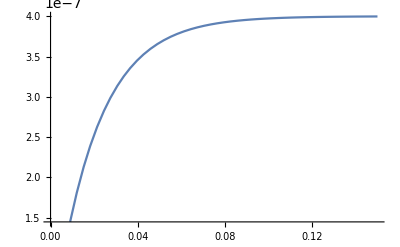

```mathematica
Plot[y/.values/.t->tt,{tt,0,0.15}]
```